# Riemann Zeta Function

### Author

Eric W. Weisstein
May 17, 2018

This notebook downloaded from http://mathworld.wolfram.com/notebooks/SpecialFunctions/RiemannZetaFunction.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/RiemannZetaFunction.html.

©2018 Wolfram Research, Inc. except for portions noted otherwise

## Plots

### Real Axis

#### V5

```mathematica
Show[GraphicsArray[{
Plot[Zeta[x],{x,-14.5,1},
PlotRange->{-.1,.1},
PlotStyle->Red,
AxesLabel->TraditionalForm/@{x,Zeta[x]},
DisplayFunction->Identity],
PlotDiscontinuous[Zeta[x],{x,-10,1,10},
VerticalAsymptotes->{1},
DisplayFunction->Identity,
AxesLabel->TraditionalForm/@{x,Zeta[x]}]
},GraphicsSpacing->-.07
]]
```

⁃GraphicsArray⁃

#### V6

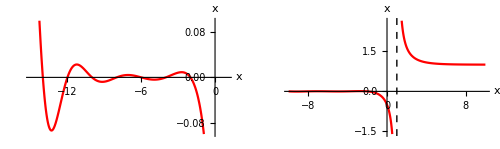

```mathematica
With[{opts=Sequence@@{PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Zeta[x]},LabelStyle->Directive[Black,FontFamily->"Times",12]}},
GraphicsRow[{
Plot[Zeta[x],{x,-15,1},PlotRange->{-.1,.1},opts],
Plot[Zeta[x],{x,-10,10},opts,Epilog->{Dashing[Small],Line[{{1,-10},{1,10}}]}]
},ImageSize->500]]
```

### Complex Plane V5

#### ReIm

```mathematica
ComplexPlot3D[Zeta[z],{z,-15,15},PlotPoints->150]//Timing
```

{35.43 Second,⁃GraphicsArray⁃}

#### Complex Plane Contour Plot

```mathematica
ComplexContourPlot[Zeta[z],{z,-15,15}]//Timing
```

{63.69 Second,⁃GraphicsArray⁃}

```mathematica
n=50;Show[GraphicsArray[ContourPlot[#[Zeta[x+I y]],{x,-n,n},{y,-n,n},PlotPoints->200,
ContourLines->False,
DisplayFunction->Identity,ColorFunction->(Hue[#]&),FrameLabel->TraditionalForm/@{x,y,#[Zeta[x+I y]],""}]&/@{Re,Im}],GraphicsSpacing->-.05]
```

⁃GraphicsArray⁃

```mathematica
Plot3D[Abs[Zeta[x+I y]],{x,0,1},{y,1,100},PlotPoints->150,Mesh->False,PlotRange->All,AxesLabel->TraditionalForm/@{x,y,""},PlotLabel->TraditionalForm[Abs[Zeta[x+I y]]]]
```

⁃SurfaceGraphics⁃

#### Complex Plane V6

```mathematica
Plot3D[Abs[Zeta[x+I y]],{x,0,1},{y,1,100},Mesh->False,PlotRange->All,PlotPoints->{10,50},MaxRecursion->4,AxesLabel->{x,y,""},PlotLabel->Abs[Zeta[x+I y]]]
```

-Graphics3D-

### Critical Line

```mathematica
ListPlot[{Re[#],Im[#]}&/@Table[Zeta[1/2+y I],{y,0,35,.05}],
PlotJoined->True,PlotRange->All,AspectRatio->Automatic,AxesLabel->TraditionalForm/@{Re[Zeta[1/2+y I]],Im[Zeta[1/2+y I]]},PlotStyle->Red]
```

⁃Graphics⁃

## Pole

```mathematica
Residue[Zeta[z],{z,1}]
```

1

## Renormalization

```mathematica
Zeta[-1]
```

-1/12

## Contour

```mathematica
Integrate[u^(z-1)/(Exp[-u]-1),{u,-∞-I ϵ,-I ϵ}]
```

∫_(-∞)^(-ⅈ ϵ) u^(-1+z)/(-1+ⅇ^-u)ⅆu

```mathematica
D[ρ Exp[I θ],θ]
```

ⅈ ⅇ^(ⅈ θ) ρ

```mathematica
Integrate[(ρ Exp[I θ])^(z-1)/(Exp[-ρ Exp[I θ]]-1)I Exp[I θ]ρ,{θ,-π/2,π/2}]
```

∫_(-π/2)^(π/2) (ⅈ ⅇ^(ⅈ θ) ρ (ⅇ^(ⅈ θ) ρ)^(-1+z))/(-1+ⅇ^(-ⅇ^(ⅈ θ) ρ))ⅆθ

```mathematica
Integrate[u^(z-1)/(Exp[-u]-1),{u,-∞+I ϵ,I ϵ}]
```

∫_(-∞)^(ⅈ ϵ) u^(-1+z)/(-1+ⅇ^-u)ⅆu

```mathematica
zeta[z_]:=With[{ϵ=10^-5,ρ=10^-5},
Plus@@{NIntegrate[u^(z-1)/(Exp[-u]-1),{u,-∞-I ϵ,-I ϵ}],
NIntegrate[(ρ Exp[I θ])^(z-1)/(Exp[-ρ Exp[I θ]]-1)I Exp[I θ]ρ,{θ,-π/2,π/2}],NIntegrate[u^(z-1)/(Exp[-u]-1),{u,I ϵ,-∞+I ϵ}]
}Gamma[1-z]/(2Pi I)
]
```

```mathematica
Through[{zeta,Zeta}[.2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in u near u = -8.99597×10^-6 - 0.00001\ ⅈ. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in u near u = -8.99597×10^-6 + 0.00001\ ⅈ. More…

{-0.733921+0. ⅈ,-0.733921}

```mathematica
Plot[{Zeta[x],zeta[x]},{x,-1.5,1.5},PlotStyle->{Red,Blue}]//Timing
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in u near u = -8.99597×10^-6 - 0.00001\ ⅈ. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in u near u = -8.99597×10^-6 + 0.00001\ ⅈ. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in u near u = -8.99597×10^-6 - 0.00001\ ⅈ. More…

General::stop: Further output of NIntegrate :: "ncvb" will be suppressed during this calculation. More…

Plot::plnr: zeta[x] is not a machine-size real number at x = -1.5. More…

Plot::plnr: zeta[x] is not a machine-size real number at x = -1.3783. More…

Plot::plnr: zeta[x] is not a machine-size real number at x = -1.24557. More…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. More…

{5. Second,⁃Graphics⁃}

## Connection with Hurwitz

```mathematica
Zeta[s,1]
```

Zeta[s]

```mathematica
TableForm[Flatten[Outer[{#1,#2,Zeta[s,#1,IncludeSingularTerm->#2]}&,{0,1},{True,False}],1],TableHeadings->{None,{"a","IncludeSingularTerm","Result"}}]
```

a | IncludeSingularTerm | Result
0 | True | Zeta[s,0,IncludeSingularTerm→True]
0 | False | Zeta[s]
1 | True | Zeta[s]
1 | False | Zeta[s]

## Powers of 10 for Positive Even

### Enumeration

```mathematica
Table[Digits[Denominator[Zeta[10^n]]],{n,0,6}]//Timing
```

{20346.8 Second,{1,5,133,2277,32660,426486,5264705}}

### Series

```mathematica
Series[Zeta[n],{n,∞,2}]
```

Zeta[n]

```mathematica
FunctionExpand[Zeta[n],n∈Integers&&n>0&&Mod[n,2]==0]
```

Zeta[n]

```mathematica
Table[1/(2^(z-1)(-1)^(1+z/2)BernoulliB[z]/z!),{z,2,10,2}]
```

{6,90,945,9450,93555}

```mathematica
expr=Log[10,(-1)^(-1-z/2)*2^(1-z)*z!];
```

```mathematica
ser=Series[expr,{z,∞,2}]
```

(-1/Log[10]-(ⅈ π)/(2 Log[10])-Log[2]/Log[10]-Log[1/z]/Log[10])/(1/z)+((ⅈ π)/Log[10]+Log[2 √(2 π)]/Log[10]-Log[1/z]/(2 Log[10]))+1/(12 Log[10] z)+O[1/z]^3

```mathematica
N[Normal[ser]/. z->10^5,10]
```

426470.7524-68217.4533 ⅈ

```mathematica
N[expr/.z->10^5,10]
```

426470.7524+1.364 ⅈ

...the series is wrong...

```mathematica
expr=Simplify[Normal[Series[Log[10,1/(2^(z-1)(-1)^(1+z/2)BernoulliB[z]/z!)],{z,∞,1}]]/.z->10^n,n∈Integers&&n>0]
```

Series::esss: Essential singularity encountered in ⅇ. More…

General::stop: Further output of Series :: "esss" will be suppressed during this calculation. More…

1/(2 Log[10])(2 ⅈ π+Log[4]+n Log[10]+10^n (-ⅈ π-2 (1+Log[2])+n Log[100])+Log[2 π]-2 Log[BernoulliB[10^n]])

```mathematica
Table[1+Floor[Re[expr]],{n,4}]
```

{5,50,498,4972}

### Primes

```mathematica
Position[Table[Denominator[Zeta[n]],{n,2,10^4,2}],_?PrimeQ]//Flatten//Timing
```

{812.677 Second,{}}

```mathematica
Position[Table[Denominator[Zeta[n]],{n,2,10^5,2}],_?PrimeQ]//Flatten//Timing
```

## Integrals

### 1/x∫_0^∞ u^(x-1)/(exp(u)-1)ⅆu==x

```mathematica
1/Gamma[x] Integrate[u^(x-1)/(Exp[u]-1),{u,0,∞}]
```

1/Gamma[x]If[Re[x]>1,Gamma[x] PolyLog[x,1],Integrate[u^(-1+x)/(-1+ⅇ^u),{u,0,∞},Assumptions→Re[x]≤1]]

```mathematica
FullSimplify[%,Re[x]>1]
```

Zeta[x]

```mathematica
FullSimplify[(Exp[-u] u^(n-1))/(1-Exp[-u])]
```

u^(-1+n)/(-1+ⅇ^u)

```mathematica
Sum[Exp[-k u] u^(n-1),{k,∞}]
```

u^(-1+n)/(-1+ⅇ^u)

### ∫_0^∞ frac(1/t) t^(s-1)ⅆt==-s/s

```mathematica
Integrate[FractionalPart[1/t] t^(s-1),{t,0,∞}]
```

∫_0^∞ t^(-1+s) FractionalPart[1/t]ⅆt

```mathematica
With[{s=.2},Plot[FractionalPart[1/t] t^(s-1),{t,0,3},PlotStyle->Red,PlotPoints->50]]
```

⁃Graphics⁃

```mathematica
With[{s=.2},Plot[FractionalPart[1/t] t^(s-1),{t,0,.5},PlotStyle->Red,PlotPoints->50]]
```

⁃Graphics⁃

```mathematica
With[{s=.2},{NIntegrate[FractionalPart[1/t] t^(s-1),{t,0,.1,.2,1,2,∞},MaxRecursion->30,Method->{"GlobalAdaptive",MaxNumberOfErrorIncreases->10^4}],-Zeta[s]/s}]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, highly oscillatory integrand, or insufficient WorkingPrecision.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the difference between the values of PrecisionGoal and WorkingPrecision is too small; the integrand is highly oscillatory or it is not a (piecewise) smooth function; the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxNumberOfErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.65222 and 0.0221806 for the integral and error estimates.

{13.8197 Second,{3.65222,3.6696}}

```mathematica
With[{s=.2},NIntegrate[FractionalPart[1/t] t^(s-1),{t,0,1,∞}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0008086810067562274`}. NIntegrate obtained 3.85832 and 0.20474 for the integral and error estimates.

3.85832

### Integral Product

```mathematica
zeta[n_]:=Module[{a=Array[x,n]},
Integrate[1/(1-Times@@a),Sequence@@({#,0,1}&/@a)]
]
```

```mathematica
Table[zeta[n],{n,2,6}]
```

{π^2/6,Zeta[3],π^4/90,Zeta[5],π^6/945}

```mathematica
Table[Zeta[n],{n,2,6}]
```

{π^2/6,Zeta[3],π^4/90,Zeta[5],π^6/945}

## Products

### ∏_n^∞ 1/(1-1/(n)^s)==s

#### V6

```mathematica
Product[(1-1/Prime[n]^s)^-1,{n,∞}]
```

Zeta[s]

## Sums

### ∑_k^∞ 1/k^n==n

```mathematica
Sum[1/k^n,{k,∞}]
```

Zeta[n]

### ∑_(n=1)^∞ 1/n^s+∑_(n=1)^∞ (-1)^n/n^s

#### V6

Re(s)>1

```mathematica
Sum[(-1)^n/n^s,{n,∞}]+Sum[1/n^s,{n,∞}]//FullSimplify
```

2^(1-s) Zeta[s]

```mathematica
2Sum[1/n^s,{n,2,∞,2}]
```

2^(1-s) Zeta[s]

```mathematica
2Sum[1/(2k)^s,{k,∞}]
```

2^(1-s) Zeta[s]

```mathematica
Simplify[Sum[(-1)^(n-1)/n^s,{n,∞}]/(1-2^(1-s))]
```

Zeta[s]

#### V7

```mathematica
Sum[(-1)^n/n^s,{n,∞}]+Sum[1/n^s,{n,∞}]//FullSimplify
```

2^(1-s) Zeta[s]

```mathematica
{SumConvergence[(-1)^n/n^s,n],SumConvergence[1/n^s,n]}
```

{Re[s]>1,Re[s]>1}

### 1/(1-2^(1-s))∑_n^∞ (-1)^(n-1)/n^s==s

```mathematica
1/(1-2^(1-s))Sum[(-1)^(n-1)/n^s,{n,∞}]//Simplify
```

Zeta[s]

### ∑_(n=0)^∞ 1/2^(n+1)∑_(k=0)^n ((-1)^k Binomial[n, k])/(k+1)^z==s

Knopp-Sondow Globally Convergent Sum

```mathematica
ζ(z)==1/(1-2^(1-z))∑_(n=0)^∞ 1/2^(n+1) ∑_(k=0)^n (-1)^k ({{n}, {k}}) (k+1)^-z
```

#### v4.2

```mathematica
zeta[z_]:=1/(1-2^(1-z))*Sum[1/2^(n+1)*Sum[((-1)^k*Binomial[n,k])/(k+1)^z,{k,0,n}],{n,0,Infinity}]
```

General::spell1: Possible spelling error: new symbol name "zeta" is similar to existing symbol "Zeta".

```mathematica
FullSimplify[{zeta[2],zeta[3],zeta[4]}]
```

{π^2/6,1/36 (4 EulerGamma (π^2-6 EulerGamma Log[2])+48 ∑_(K$508=0)^∞ (2^(-2-K$508) PolyGamma[0,2+K$508]^2)/(1+K$508)+15 Zeta[3]),8/7 ∑_(n=0)^∞ 2^(-1-n) ∑_(k=0)^n ((-1)^k Binomial[n,k])/(1+k)^4}

```mathematica
N[%]
```

{1.64493,1.20206,1.08232}

#### v5.0

```mathematica
Sum[((-1)^k*Binomial[n,k])/(k+1)^z,{k,0,n}]
```

∑_(k=0)^n (-1)^k (1+k)^-z Binomial[n,k]

```mathematica
With[{z=2},Sum[((-1)^k*Binomial[n,k])/(k+1)^z,{k,0,n}]]
```

EulerGamma/(1+n)+PolyGamma[0,2+n]/(1+n)

```mathematica
With[{z=4},Sum[((-1)^k*Binomial[n,k])/(k+1)^z,{k,0,n}]]
```

1/(12 (1+n))(6 EulerGamma PolyGamma[0,2+n]^2+2 PolyGamma[0,2+n]^3+PolyGamma[0,2+n] (6 EulerGamma^2+π^2-6 PolyGamma[1,2+n])-6 EulerGamma PolyGamma[1,2+n]+2 PolyGamma[2,2+n])+(2 EulerGamma^3+EulerGamma π^2+4 Zeta[3])/(12 (1+n))

```mathematica
zeta[z_]:=1/(1-2^(1-z))*Sum[1/2^(n+1)*Sum[((-1)^k*Binomial[n,k])/(k+1)^z,{k,0,n}],{n,0,Infinity}]
```

General::spell1: Possible spelling error: new symbol name "zeta" is similar to existing symbol "Zeta". More…

```mathematica
zeta[s]
```

(∑_(n=0)^∞ 2^(-1-n) ∑_(k=0)^n (-1)^k (1+k)^-s Binomial[n,k])/(1-2^(1-s))

```mathematica
FullSimplify[{zeta[2],zeta[3],zeta[4]}]
```

{π^2/6,4/3 ∑_(n=0)^∞ 1/(3 (1+n))(2^(-3-n) (6 EulerGamma^2+π^2+12 EulerGamma PolyGamma[0,2+n]+6 PolyGamma[0,2+n]^2-6 PolyGamma[1,2+n])),8/7 ∑_(n=0)^∞ 1/(3 (1+n))(2^(-3-n) (2 EulerGamma^3+EulerGamma π^2+(6 EulerGamma^2+π^2) PolyGamma[0,2+n]+6 EulerGamma PolyGamma[0,2+n]^2+2 PolyGamma[0,2+n]^3-6 EulerGamma PolyGamma[1,2+n]-6 PolyGamma[0,2+n] PolyGamma[1,2+n]+2 PolyGamma[2,2+n]+4 Zeta[3]))}

```mathematica
N[%]
```

{1.64493,1.20206,1.08232}

Table

```mathematica
Table[Zeta[n],{n,2,4}]
```

{π^2/6,Zeta[3],π^4/90}

```mathematica
N[%]
```

{1.64493,1.20206,1.08232}

#### v6.0

```mathematica
zeta[z_]:=1/(1-2^(1-z))*Sum[1/2^(n+1)*Sum[((-1)^k*Binomial[n,k])/(k+1)^z,{k,0,n}],{n,0,Infinity}]
```

```mathematica
zeta[s]
```

(∑_(n=0)^∞ 2^(-1-n) ∑_(k=0)^n (-1)^k (1+k)^-s Binomial[n,k])/(1-2^(1-s))

```mathematica
zeta/@Range[2,4]
```

{1/3 (-π^2+6 ⅈ π Log[2]+6 PolyLog[2,2]),4/3 ∑_(n=0)^∞ 2^(-1-n) ((6 EulerGamma^2+π^2)/(12 (1+n))+1/(2+2 n)(2 EulerGamma PolyGamma[0,2+n]+PolyGamma[0,2+n]^2-PolyGamma[1,2+n])),8/7 ∑_(n=0)^∞ 2^(-1-n) (1/(12 (1+n))(6 EulerGamma PolyGamma[0,2+n]^2+2 PolyGamma[0,2+n]^3+PolyGamma[0,2+n] (6 EulerGamma^2+π^2-6 PolyGamma[1,2+n])-6 EulerGamma PolyGamma[1,2+n]+2 PolyGamma[2,2+n])+(2 EulerGamma^3+EulerGamma π^2+4 Zeta[3])/(12 (1+n)))}

```mathematica
FullSimplify[First[%]]
```

π^2/6

### 1/(s-1)∑_(n=0)^∞ 1/(n+1)∑_(k=0)^n (-1)^k (k+1)^(1-s) Binomial[n, k]==s

Hasse Globally Convergent Sum

```mathematica
zeta[s_]:=1/(s-1)Sum[1/(n+1)Sum[(-1)^k Binomial[n,k](k+1)^(1-s),{k,0,n}],{n,0,∞}]
```

#### V6.0

```mathematica
zeta/@Range[2,5]
```

Sum::div: Sum does not converge. More…

{π^2/6,Zeta[3],1/3 ∑_(n=0)^∞ 1/(1+n)((6 EulerGamma^2+π^2)/(12 (1+n))+1/(2+2 n)(2 EulerGamma PolyGamma[0,2+n]+PolyGamma[0,2+n]^2-PolyGamma[1,2+n])),1/4 ∑_(n=0)^∞ 1/(1+n)(1/(12 (1+n))(6 EulerGamma PolyGamma[0,2+n]^2+2 PolyGamma[0,2+n]^3+PolyGamma[0,2+n] (6 EulerGamma^2+π^2-6 PolyGamma[1,2+n])-6 EulerGamma PolyGamma[1,2+n]+2 PolyGamma[2,2+n])+(2 EulerGamma^3+EulerGamma π^2+4 Zeta[3])/(12 (1+n)))}

```mathematica
FullSimplify[1/(1+n)((6 EulerGamma^2+π^2)/(12 (1+n))+1/(2+2 n)(2 EulerGamma PolyGamma[0,2+n]+PolyGamma[0,2+n]^2-PolyGamma[1,2+n])),n∈Integers&&n>1]
```

(π^2+6 HarmonicNumber[1+n]^2-6 PolyGamma[1,2+n])/(12 (1+n)^2)

```mathematica
Sum[%,{n,0,∞}]
```

Sum::div: Sum does not converge. More…

∑_(n=0)^∞ (π^2+6 HarmonicNumber[1+n]^2-6 PolyGamma[1,2+n])/(12 (1+n)^2)

```mathematica
1/3 NSum[(π^2+6 HarmonicNumber[1+n]^2-6 PolyGamma[1,2+n])/(12 (1+n)^2),{n,0,∞}]
```

1.08232

```mathematica
Zeta[4.]
```

1.08232

#### V6.1

```mathematica
1/(n+1)Sum[(-1)^k Binomial[n,k](k+1)^(1-s),{k,0,n}]
```

(∑_(k=0)^n (-1)^k (1+k)^(1-s) Binomial[n,k])/(1+n)

```mathematica
Print[{#,zeta[#]//Timing}]&/@Range[2,4]
```

{2,{0.000678,π^2/6}}

{3,{0.000595,Zeta[3]}}

{4,{93.2301,1/3 ∑_(n=0)^∞ 1/(12 (1+n)^2)(6 EulerGamma^2+π^2+12 EulerGamma PolyGamma[0,2+n]+6 PolyGamma[0,2+n]^2-6 PolyGamma[1,2+n])}}

{Null,Null,Null}

```mathematica
Sum[(π^2+6 HarmonicNumber[1+n]^2-6 PolyGamma[1,2+n])/(12 (1+n)^2),{n,0,∞}]
```

π^4/30

### ∑_(n=0)^∞ ((-1)^n (s-1)^n n)/(n!)+1/(s-1)==s

```mathematica
1/(s-1)+Sum[(-1)^n/(n!)StieltjesGamma[n](s-1)^n,{n,0,∞}]
```

Zeta[s]

### ∑_n^∞ n/n^s==(2 s)/s

```mathematica
Sum[LiouvilleLambda[n]/n^s,{n,∞}]
```

Zeta[2 s]/Zeta[s]

### ∑_n^∞ 2^n/n^s==s^2/(2 s)

```mathematica
Sum[2^PrimeNu[n]/n^s,{n,∞}]//Timing
```

{7.46028,∑_n^∞ 2^PrimeNu[n] n^-s}

### 1/2 ∑_(k=1)^∞ H_k/k^2==ζ(3)

```mathematica
1/2 Sum[HarmonicNumber[k]/k^2,{k,∞}]
```

Zeta[3]

### lim_(x→∞) (∑_(k=1)^x cot^n(k/(2 x+1)))/(2 x+1)^n==ζ(n)

Stark Identities

```mathematica
s[n_,x_]:=1/(2x+1)^n  Sum[Cot[k/(2x+1)]^n,{k,x}]
```

#### V6.0

```mathematica
sn[n_,x_]:=1/(2x+1)^n NSum[Cot[k/(2x+1)]^n,{k,x}]
```

```mathematica
Table[{sn[n,10000],Zeta[n]//N},{n,3,7,2}]
```

{{1.20206,1.20206},{1.03693,1.03693},{1.00835,1.00835}}

```mathematica
Limit[1/(2x+1)^n Sum[Cot[k/(2x+1)]^n,{k,x}],x->∞]
```

Limit[(1+2 x)^-n ∑_(k=1)^x Cot[k/(1+2 x)]^n,x→∞]

```mathematica
Table[Limit[1/(2x+1)^n Sum[Cot[k/(2x+1)]^n,{k,x}],x->∞],{n,2,3}]
```

{Limit[(∑_(k=1)^x Cot[k/(1+2 x)]^2)/(1+2 x)^2,x→∞],Limit[(∑_(k=1)^x Cot[k/(1+2 x)]^3)/(1+2 x)^3,x→∞]}

### ∑_(n=1)^∞ (μ(n))/n^s==1/(ζ(s))

```mathematica
Sum[MoebiusMu[n]/n^s,{n,∞}]
```

1/Zeta[s]

### -∑_k^∞ (log(k))/k^s==ζ'(s)

```mathematica
-Sum[Log[k]/k^s,{k,∞}]
```

Zeta'[s]

### -∑_(k=2)^∞ (log(k))/k^s==ζ'(s)

```mathematica
-Sum[Log[k]/k^s,{k,2,∞}]
```

Zeta'[s]

### ∑_k^∞ ((-1)^k (s-1)^(k-1) k)/(k!)-1/(s-1)^2==ζ'(s)

#### V7

```mathematica
sum=-1/(s-1)^2+Sum[1/(k!)StieltjesGamma[k](-1)^k(s-1)^(k-1),{k,∞}]
```

-1/(-1+s)^2+(-EulerGamma-1/(-1+s)+Zeta[s])/(-1+s)

...wrong...

```mathematica
SumConvergence[1/(k!)StieltjesGamma[k](-1)^k(s-1)^(k-1),k]
```

1/(-1+s)==0

...wrong..

```mathematica
FullSimplify[sum,s>1]
```

(-2+EulerGamma-EulerGamma s+(-1+s) Zeta[s])/(-1+s)^2

```mathematica
sum/.s->4.
```

-0.053853

```mathematica
Zeta'[4.]
```

-0.0689113

```mathematica
s1=-1/(s-1)^2+Sum[1/((k-1)!)StieltjesGamma[k](-1)^k(s-1)^(k-1),{k,5}]
```

-1/(-1+s)^2-StieltjesGamma[1]+(-1+s) StieltjesGamma[2]-1/2 (-1+s)^2 StieltjesGamma[3]+1/6 (-1+s)^3 StieltjesGamma[4]-1/24 (-1+s)^4 StieltjesGamma[5]

```mathematica
s2=Series[Zeta'[s],{s,1,4}]
```

-1/(s-1)^2-StieltjesGamma[1]+StieltjesGamma[2] (s-1)-1/2 StieltjesGamma[3] (s-1)^2+1/6 StieltjesGamma[4] (s-1)^3-1/24 StieltjesGamma[5] (s-1)^4+O[s-1]^5

```mathematica
s1-s2
```

O[s-1]^5

### nodd, n ≡ 3 (mod 4)

```mathematica
(2^(n-1)π^n)/((n+1)!)Sum[(-1)^(k-1)Binomial[n+1,2k]BernoulliB[n+1-2k]BernoulliB[2k],{k,0,(n+1)/2}]-2Sum[1/(k^n(Exp[2π k]-1)),{k,∞}]
```

-2 ∑_(k=1)^∞ k^-n/(-1+ⅇ^(2 k π))+1/((1+n)!)2^(-1+n) π^n ∑_(k=0)^((1+n)/2) (-1)^(-1+k) BernoulliB[2 k] BernoulliB[1-2 k+n] Binomial[1+n,2 k]

```mathematica
Subtract@@@Table[{Zeta[n],(2^(n-1)π^n)/((n+1)!)Sum[(-1)^(k-1)Binomial[n+1,2k]BernoulliB[n+1-2k]BernoulliB[2k],{k,0,(n+1)/2}]-2Sum[1/(k^n(Exp[2π k]-1)),{k,∞}]},{n,3,50,4}]//N[#,20]&
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {-7 π^3/180 + 2 ∑ k = 1 ∞ 1/(-1 + Power[« 2 »]) k^3 + Zeta[3], -19 π^7/56700 + 2 ∑ k = 1 ∞ 1/(-1 + Power[« 2 »]) k^7 + Zeta[7], « 8 », « 2 »}. More…

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### nodd, n ≡ 1 (mod 4)

```mathematica
(2π)^n/((n+1)!(n-1))Sum[(-1)^k(n+1-4k)Binomial[n+1,2k]BernoulliB[n+1-2k]BernoulliB[2k],{k,0,(n+1)/4}]-2Sum[(Exp[2π k](1+(4π k)/(n-1))-1)/(k^n(Exp[2π k]-1)^2),{k,∞}]
```

-2 ∑_(k=1)^∞ (k^-n (-1+ⅇ^(2 k π) (1+(4 k π)/(-1+n))))/((-1+ⅇ^(2 k π))^2)+1/((-1+n) (1+n)!)(2 π)^n ∑_(k=0)^((1+n)/4) (-1)^k (1-4 k+n) BernoulliB[2 k] BernoulliB[1-2 k+n] Binomial[1+n,2 k]

```mathematica
Table[{Zeta[n],(2π)^n/((n+1)!(n-1))Sum[(-1)^k(n+1-4k)Binomial[n+1,2k]BernoulliB[n+1-2k]BernoulliB[2k],{k,0,(n+1)/4}]-2Sum[(Exp[2π k](1+(4π k)/(n-1))-1)/(k^n(Exp[2π k]-1)^2),{k,∞}]},{n,5,20,4}]
```

{{Zeta[5],(13 π^5)/3780-2 ∑_(k=1)^∞ (-1+ⅇ^(2 k π) (1+k π))/((-1+ⅇ^(2 k π))^2 k^5)},{Zeta[9],(127 π^9)/3742200-2 ∑_(k=1)^∞ (-1+ⅇ^(2 k π) (1+(k π)/2))/((-1+ⅇ^(2 k π))^2 k^9)},{Zeta[13],(3989 π^13)/11493231750-2 ∑_(k=1)^∞ (-1+ⅇ^(2 k π) (1+(k π)/3))/((-1+ⅇ^(2 k π))^2 k^13)},{Zeta[17],(94861 π^17)/26652509730000-2 ∑_(k=1)^∞ (-1+ⅇ^(2 k π) (1+(k π)/4))/((-1+ⅇ^(2 k π))^2 k^17)}}

```mathematica
%//N
```

{{1.03693,1.03693},{1.00201,1.00201},{1.00012,1.00012},{1.00001,1.00001}}

### ∑_(k=0)^n ((-1)^k (n k))/(k+1)^4

```mathematica
Sum[((-1)^k*Binomial[n, k])/(k + 1)^4, {k, 0, n}]
```

1/(12 (1+n))(6 EulerGamma PolyGamma[0,2+n]^2+2 PolyGamma[0,2+n]^3+PolyGamma[0,2+n] (6 EulerGamma^2+π^2-6 PolyGamma[1,2+n])-6 EulerGamma PolyGamma[1,2+n]+2 PolyGamma[2,2+n])+(2 EulerGamma^3+EulerGamma π^2+4 Zeta[3])/(12 (1+n))

```mathematica
FullSimplify[%]
```

1/(12 (1+n))(2 HarmonicNumber[1+n]^3+HarmonicNumber[1+n] (π^2-6 PolyGamma[1,2+n])+2 (PolyGamma[2,2+n]+2 Zeta[3]))

### 3 ∑_(k=1)^∞ 1/(k^2 (2 k k))==ζ(2)

```mathematica
{3Sum[1/(k^2 Binomial[2k,k]),{k,∞}],Zeta[2]}
```

{π^2/6,π^2/6}

### 5/2 ∑_(k=1)^∞ (-1)^(k-1)/(k^3 (2 k k))==ζ(3)

```mathematica
{5/2Sum[(-1)^(k-1)/(k^3 Binomial[2k,k]),{k,∞}],Zeta[3]}
```

{Zeta[3],Zeta[3]}

### 36/17 ∑_(k=1)^∞ 1/(k^4 (2 k k))==ζ(4)

#### v5.2

```mathematica
36/17Sum[1/(k^4 Binomial[2k,k]),{k,∞}]
```

18/17 HypergeometricPFQ[{1,1,1,1,1},{3/2,2,2,2},1/4]

#### v6

```mathematica
{36/17Sum[1/(k^4 Binomial[2k,k]),{k,∞}],Zeta[4]}
```

{π^4/90,π^4/90}

### ∑_(n=2)^∞ (ζ(n)-1)==1

```mathematica
Sum[Zeta[n]-1,{n,2,∞}]
```

1

### -16/11∑_(n=1)^∞ ((2 (-1)^n+1) H_n)/n^4==ζ(5)

```mathematica
-16/11 Sum[((2(-1)^n+1)HarmonicNumber[n])/n^4,{n,∞}]//FullSimplify
```

2/165 (EulerGamma π^4-240 HypergeometricPFQRegularized^({0,0,0,0,0},{0,0,0,1},0)[{1,1,1,1,1},{2,2,2,2},-1]+120 HypergeometricPFQRegularized^({0,0,0,0,0},{0,0,0,1},0)[{1,1,1,1,1},{2,2,2,2},1])

```mathematica
-16/11 NSum[((2(-1)^n+1)HarmonicNumber[n])/n^4,{n,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in n near {n} = {91.0791}. NIntegrate obtained 0.000303439  + 0.0000318175\ ⅈ and 4.58741×10^-6 for the integral and error estimates.

1.03693+1.07292×10^-6 ⅈ

```mathematica
Zeta[5.]
```

1.03693

### ∑_(n=2, 4, …)^∞ (ζ(n)-1)==3/4

```mathematica
Sum[Zeta[n]-1,{n,2,∞,2}]
```

3/4

### ∑_(n=3, 5, …)^∞ (ζ(n)-1)==1/4

```mathematica
Sum[Zeta[n]-1,{n,3,∞,2}]
```

1/4

### ∑_(n=2)^∞ (-1)^n(ζ(n)-1)==1/2

```mathematica
Sum[(-1)^n(Zeta[n]-1),{n,2,∞}]
```

1/2

### ∑_(n=1)^∞ (ζ(k n)-1)

```mathematica
Sum[Zeta[2k]-1,{k,∞}]//FullSimplify
```

3/4

```mathematica
Sum[Zeta[3k]-1,{k,∞}]//FullSimplify
```

1/3 (-(-1)^(2/3) HarmonicNumber[1/2 (3-ⅈ √3)]+(-1)^(1/3) HarmonicNumber[1/2 (3+ⅈ √3)])

```mathematica
Sum[Zeta[4k]-1,{k,∞}]
```

1/8 Csch[π] (-2 π Cosh[π]+7 Sinh[π])

```mathematica
FullSimplify[%]
```

1/8 (7-2 π Coth[π])

```mathematica
Sum[Zeta[5k]-1,{k,∞}]//FullSimplify
```

∑_(k=1)^∞ (-1+Zeta[5 k])

```mathematica
Sum[Zeta[6k]-1,{k,∞}]//FullSimplify
```

∑_(k=1)^∞ (-1+Zeta[6 k])

### ∑_(k=2)^∞ (ζ(k)-1)/k==1-ℽ

```mathematica
Sum[(Zeta[k]-1)/k,{k,2,∞}]
```

1-EulerGamma

### ∑_(k=2)^∞ (ζ(k) (-1)^k)/k==ℽ

### ∑_(k=2)^∞ ((-n)^k k)/k==ℽ n+log(n+1)

#### V6

```mathematica
Sum[((-n)^k Zeta[k])/k,{k,2,∞}]
```

Log[Gamma[1+n]]+1/2 (-EulerGamma-2 EulerGamma Zeta[0,1+n])

```mathematica
FullSimplify[%,-1<n≤1]
```

EulerGamma n+Log[Gamma[1+n]]

#### V7

```mathematica
Sum[((-n)^k Zeta[k])/k,{k,2,∞}]
```

EulerGamma n+Log[Gamma[1+n]]

### ∑_(n=1)^∞ (ζ(2 n))/(n (2 n+1) 2^(2 n))==log(π)-1

```mathematica
Sum[Zeta[2n]/(n(2n+1)2^(2n)),{n,∞}]
```

-1+Log[π]

### ∑_(n=1)^∞ (ζ(2 n))/(n (2 n+1))==log(2 π)-1

```mathematica
Sum[Zeta[2n]/(n(2n+1)),{n,∞}]//Simplify
```

-1+Log[2]+Log[π]

### ∑_(k=1)^∞ (ζ(2 k,z))/(k (2 k+1) 2^(2 k))==-2 z+(2 z-1) log(z-1/2)-2 log(z)+log(2 π)+1

```mathematica
Sum[Zeta[2k,z]/(k(2k+1)2^(2k)),{k,∞}]//FullSimplify
```

1-2 z+Log[2 π]+(-1+2 z) Log[-1/2+z]-2 Log[Gamma[z]]

### ∑_(k=2)^(n-2) (ζ(k) ζ(n-k))/2^k

B. Cloitre, Dec 11–13, 2005

```mathematica
Sum[Zeta[k] x^(k-1),{k,2,∞}]
```

-EulerGamma-PolyGamma[0,1-x]

```mathematica
Sum[(Zeta[k]Zeta[n-k])/2^k,{k,2,n-2}]
```

∑_(k=2)^(-2+n) 2^-k Zeta[k] Zeta[-k+n]

```mathematica
Table[Sum[(Zeta[k]Zeta[n-k])/2^k,{k,2,n-2}],{n,3,10}]//TableForm//TraditionalForm
```

0
π^4/144
1/16 π^2 ζ(3)
π^6/1728+(ζ(3))^2/8
1/480 π^4 ζ(3)+3/64 π^2 ζ(5)
(11 π^8)/201600+5/32 ζ(3) ζ(5)
(π^6 ζ(3))/6720+1/960 π^4 ζ(5)+11/256 π^2 ζ(7)
(47 π^10)/8709120+(ζ(5))^2/32+17/128 ζ(3) ζ(7)

```mathematica
Table[Sum[(Zeta[k]Zeta[n-k])/2^k,{k,2,n-2}],{n,3,20}]//N
```

{0.,0.676452,0.741489,0.736977,0.723662,0.712485,0.704811,0.699967,0.697048,0.695343,0.694367,0.693818,0.693513,0.693346,0.693254,0.693204,0.693178,0.693163}

### ∑_(k=1)^∞ 1/(k (k+1))^(2m+1)== -2 ∑_(k=0)^m Binomial[4 m-2k+1, 2 m] Zeta(2 k)

```mathematica
Sum[1/(k(k+1))^(2m+1),{k,∞}]
```

∑_k^∞ (k (1+k))^(-1-2 m)

#### m==1

```mathematica
sum=Sum[1/(k(k+1))^3,{k,∞}]
```

10-π^2

```mathematica
CoefficientList[sum,π^2]/Zeta[2Range[0,1]]/.π->1
```

{-20,-6}

```mathematica
%.Zeta[2Range[0,1]]
```

10-π^2

#### m==2

```mathematica
sum=Sum[1/(k(k+1))^5,{k,∞}]//Expand
```

126-(35 π^2)/3-π^4/9

```mathematica
CoefficientList[sum,π^2]/Zeta[2Range[0,2]]/.π->1
```

{-252,-70,-10}

#### m==3

```mathematica
sum=Sum[1/(k(k+1))^7,{k,∞}]
```

-2/135 (-115830+10395 π^2+126 π^4+π^6)

```mathematica
CoefficientList[sum,π^2]/Zeta[2Range[0,3]]/.π->1
```

{-3432,-924,-168,-14}

#### m==4

```mathematica
sum=Sum[1/(k(k+1))^9,{k,∞}]
```

(38288250-3378375 π^2-45045 π^4-550 π^6-3 π^8)/1575

```mathematica
CoefficientList[sum,π^2]/Zeta[2Range[0,4]]/.π->1
```

{-48620,-12870,-2574,-330,-18}

#### m==5

```mathematica
sum=Sum[1/(k(k+1))^11,{k,∞}]
```

-(2 (-7499623950+654729075 π^2+9189180 π^4+135135 π^6+1287 π^8+5 π^10))/42525

```mathematica
CoefficientList[sum,π^2]/Zeta[2Range[0,5]]/.π->1
```

{-705432,-184756,-38896,-6006,-572,-22}

#### m==6

```mathematica
sum=Sum[1/(k(k+1))^13,{k,∞}]
```

-1/49116375 2 (-127709942456250+11068195012875 π^2+160408623375 π^4+2618916300 π^6+32162130 π^8+238875 π^10+691 π^12)

```mathematica
CoefficientList[sum,π^2]/Zeta[2Range[0,6]]/.π->1
```

{-10400600,-2704156,-587860,-100776,-12376,-910,-26}

#### Initial term

```mathematica
2Table[Binomial[4n+1,2n],{n,6}]
```

{20,252,3432,48620,705432,10400600}

```mathematica
FindSequenceFunction[{20,252,3432,48620,705432,10400600},n]
```

FindSequenceFunction[{20,252,3432,48620,705432,10400600},n]

#### 2nd Term

```mathematica
2Table[Binomial[4n-1,2n],{n,6}]
```

{6,70,924,12870,184756,2704156}

#### 3rd term

```mathematica
seq={168,2574,38896,587860}
```

{168,2574,38896,587860}

```mathematica
2Table[Binomial[4n-3,2n],{n,6}]
```

{0,10,168,2574,38896,587860}

#### Last term

```mathematica
Table[4n+2,{n,5}]
```

{6,10,14,18,22}

```mathematica
Binomial[4n+2,4n+1]
```

2+4 n

#### Closed form

```mathematica
Table[-2Sum[Inactive[Zeta][2k]Binomial[4m-2k+1,2m],{k,0,m}],{m,6}]//Expand//Column
```

-20 Zeta[0]-6 Zeta[2]
-252 Zeta[0]-70 Zeta[2]-10 Zeta[4]
-3432 Zeta[0]-924 Zeta[2]-168 Zeta[4]-14 Zeta[6]
-48620 Zeta[0]-12870 Zeta[2]-2574 Zeta[4]-330 Zeta[6]-18 Zeta[8]
-705432 Zeta[0]-184756 Zeta[2]-38896 Zeta[4]-6006 Zeta[6]-572 Zeta[8]-22 Zeta[10]
-10400600 Zeta[0]-2704156 Zeta[2]-587860 Zeta[4]-100776 Zeta[6]-12376 Zeta[8]-910 Zeta[10]-26 Zeta[12]

```mathematica
Table[Sum[1/(k(k+1))^(2m+1),{k,∞}]
```

```mathematica
Subtract@@@Table[{Sum[1/(k(k+1))^(2m+1),{k,∞}],-2Sum[Zeta[2k]Binomial[4m-2k+1,2m],{k,0,m}]},{m,6}]//Expand//Timing
```

{0.002304,{0,0,0,0,0,0}}

```mathematica
With[{m=7},-2Sum[Zeta[2k]Binomial[4m-2k+1,2m],{k,0,m}]]
```

-2 (-38779380+3343050 π^2+(148580 π^4)/3+(163438 π^6)/189+(1292 π^8)/105+(1292 π^10)/10395+(93976 π^12)/127702575+(2 π^14)/1216215)

```mathematica
Expand[%-With[{m=7},Sum[1/(k(k+1))^(2m+1),{k,∞}]]]//Timing
```

{182.878,0}

## Integer Arguments

### Positive Even

```mathematica
Table[Zeta[n],{n,2,10,2}]
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555}

```mathematica
Table[2^(n-1)Abs[BernoulliB[n]]Pi^n/n!,{n,2,10,2}]
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555}

```mathematica
Table[2^(n-1)(-1)^(1+n/2)BernoulliB[n]Pi^n/n!,{n,2,10,2}]
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555}

```mathematica
FunctionExpand[Zeta[n],n∈Integers&&n>0&&Mod[n,2]==0]
```

Zeta[n]

### Negative Odd

```mathematica
Table[Zeta[n],{n,-1,-10,-2}]
```

{-1/12,1/120,-1/252,1/240,-1/132}

```mathematica
Table[-BernoulliB[-n+1]/(-n+1),{n,-1,-10,-2}]
```

{-1/12,1/120,-1/252,1/240,-1/132}

```mathematica
FunctionExpand[Zeta[n],n∈Integers&&n<0&&Mod[n,2]==1]
```

Zeta[n]

## Apéry-Type Sums

```mathematica
Sum[1/j^n,{j,k-1}]
```

HarmonicNumber[-1+k,n]

### Even n

```mathematica
Sum[1/(k^2-x^2),{k,∞}]//Simplify
```

(1-π x Cot[π x])/(2 x^2)

```mathematica
Sum[Zeta[2n+2] x^(2n),{n,0,∞}]
```

(Csc[π √(x^2)] (-π √(x^2) Cos[π √(x^2)]+Sin[π √(x^2)]))/(2 x^2)

```mathematica
Simplify[%,x>0]
```

(1-π x Cot[π x])/(2 x^2)

```mathematica
Product[(1-(4 x^2)/m^2)/(1-x^2/m^2),{m,k-1}]//FullSimplify
```

(Cos[π x] Gamma[k-2 x] Gamma[k+2 x])/(Gamma[k-x] Gamma[k+x])

```mathematica
3Sum[1/(k^2 Binomial[2k,k](1-x^2/k^2))(Cos[π x] Gamma[k-2 x] Gamma[k+2 x])/(Gamma[k-x] Gamma[k+x]),{k,∞}]
```

-(3 HypergeometricPFQ[{1,2,1-2 x,1+2 x},{3/2,2-x,2+x},1/4])/(2 (-1+x^2))

```mathematica
Series[-(3 HypergeometricPFQ[{1,2,1-2 x,1+2 x},{3/2,2-x,2+x},1/4])/(2 (-1+x^2)),{x,0,4}]
```

HypergeometricPFQ[{1,2,1-2 x+O[x]^5,1+2 x+O[x]^5},{3/2,2-x+O[x]^5,2+x+O[x]^5},1/4] (3/2+(3 x^2)/2+(3 x^4)/2+O[x]^5)

### ζ(5)

```mathematica
Zeta[5]//N
```

1.03693

```mathematica
2NSum[(-1)^(k+1)/(k^5 Binomial[2k,k]),{k,∞}]-5/2 NSum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,2],{k,∞}]
```

1.03693

```mathematica
2Sum[(-1)^(k+1)/(k^5 Binomial[2k,k]),{k,∞}]-5/2 Sum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,2],{k,∞}]//Timing
```

{331.178 Second,HypergeometricPFQ[{1,1,1,1,1,1},{3/2,2,2,2,2},-1/4]-5/2 ∑_(k=1)^∞ ((-1)^(1+k) HarmonicNumber[-1+k,2])/(k^3 Binomial[2 k,k])}

### ζ(7)

```mathematica
Zeta[7]//N
```

1.00835

```mathematica
5/2 NSum[(-1)^(k+1)/(k^7 Binomial[2k,k]),{k,∞}]+25/2 NSum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,4],{k,∞}]
```

1.00835

```mathematica
5/2 Sum[(-1)^(k+1)/(k^7 Binomial[2k,k]),{k,∞}]+25/2 Sum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,4],{k,∞}]//Timing
```

{236.54 Second,5/4 HypergeometricPFQ[{1,1,1,1,1,1,1,1},{3/2,2,2,2,2,2,2},-1/4]+25/2 ∑_(k=1)^∞ ((-1)^(1+k) HarmonicNumber[-1+k,4])/(k^3 Binomial[2 k,k])}

### ζ(9)

```mathematica
Zeta[9]//N
```

1.00201

```mathematica
9/4 NSum[(-1)^(k+1)/(k^9 Binomial[2k,k]),{k,∞}]-5/4 NSum[(-1)^(k+1)/(k^7 Binomial[2k,k])HarmonicNumber[-1+k,2],{k,∞}]+5NSum[(-1)^(k+1)/(k^5 Binomial[2k,k])HarmonicNumber[-1+k,4],{k,∞}]+45/4 NSum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,6],{k,∞}]-25/4 NSum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,4]HarmonicNumber[-1+k,2],{k,∞}]
```

1.00201

```mathematica
9/4 Sum[(-1)^(k+1)/(k^9 Binomial[2k,k]),{k,∞}]-5/4 Sum[(-1)^(k+1)/(k^7 Binomial[2k,k])HarmonicNumber[-1+k,2],{k,∞}]+5Sum[(-1)^(k+1)/(k^5 Binomial[2k,k])HarmonicNumber[-1+k,4],{k,∞}]+45/4 Sum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,6],{k,∞}]-25/4 Sum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,4]HarmonicNumber[-1+k,2],{k,∞}]//Timing
```

### ζ(11)

```mathematica
Zeta[11]//N
```

1.00049

```mathematica
5/2 NSum[(-1)^(k+1)/(k^11 Binomial[2k,k]),{k,∞}]+25/2 NSum[(-1)^(k+1)/(k^7 Binomial[2k,k])HarmonicNumber[-1+k,4],{k,∞}]-75/4 NSum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,8],{k,∞}]+125/4 NSum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,4]^2,{k,∞}]
```

1.00049

```mathematica
5/2 Sum[(-1)^(k+1)/(k^11 Binomial[2k,k]),{k,∞}]+25/2 Sum[(-1)^(k+1)/(k^7 Binomial[2k,k])HarmonicNumber[-1+k,4],{k,∞}]-75/4 Sum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,8],{k,∞}]+125/4 Sum[(-1)^(k+1)/(k^3 Binomial[2k,k])HarmonicNumber[-1+k,4]^2,{k,∞}]//Timing
```

{679.518 Second,5/4 HypergeometricPFQ[{1,1,1,1,1,1,1,1,1,1,1,1},{3/2,2,2,2,2,2,2,2,2,2,2},-1/4]+25/2 ∑_(k=1)^∞ ((-1)^(1+k) HarmonicNumber[-1+k,4])/(k^7 Binomial[2 k,k])+125/4 ∑_(k=1)^∞ ((-1)^(1+k) HarmonicNumber[-1+k,4]^2)/(k^3 Binomial[2 k,k])-75/4 ∑_(k=1)^∞ ((-1)^(1+k) HarmonicNumber[-1+k,8])/(k^3 Binomial[2 k,k])}

## Sums with No Known Closed Forms

### ∑_(n=2)^∞ (ζ(n))/(n!)

Converges

#### Numeric

```mathematica
NSum[Zeta[n]/n!,{n,2,Infinity},WorkingPrecision->50]
```

1.07818872957581848275826543676983238

#### v5

```mathematica
Sum[Zeta[n]/n!,{n,2,∞}]
```

∑_(n=2)^∞ Zeta[n]/(n!)

```mathematica
Sum[1/n!/Gamma[n]u^(n-1)/(E^u-1),{n,2,∞}]
```

(-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u)

```mathematica
FullSimplify[%]
```

(-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u)

```mathematica
Integrate[(-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u),{u,0,∞}]
```

Integrate::gener: Unable to check convergence. (More…)

Integrate::idiv: Integral of 1/1 - ⅇ^u - BesselI[1, 2\ √u]/(1 - ⅇ^u)\ √u does not converge on {0, ∞}. (More…)

∫_0^∞ (-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u)ⅆu

```mathematica
NIntegrate[(-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u),{u,0,10,∞},WorkingPrecision->120,MaxRecursion->20]//Timing
```

NIntegrate::singd: NIntegrate's singularity handling has failed at point {u}={1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793} for the specified precision goal. Try using larger values for any of $MaxExtraPrecision or the options WorkingPrecision, or SingularityDepth and MaxRecursion. More…

NIntegrate::inum: Integrand -u + √u\ BesselI[1, 2\ √u]/(-1 + ⅇ^u)\ u is not numerical at {u} = {1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793}. More…

NIntegrate::singd: NIntegrate's singularity handling has failed at point {u}={1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793} for the specified precision goal. Try using larger values for any of $MaxExtraPrecision or the options WorkingPrecision, or SingularityDepth and MaxRecursion. More…

NIntegrate::inum: Integrand -u + √u\ BesselI[1, 2\ √u]/(-1 + ⅇ^u)\ u is not numerical at {u} = {1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793}. More…

{1.93148 Second,NIntegrate[(-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u),{u,0,10,∞},WorkingPrecision→120,MaxRecursion→20]}

```mathematica
Integrate[(-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u),{u,0,∞}]
```

∫_0^∞ (-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u)ⅆu

```mathematica
NIntegrate[(-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u),{u,0,10,∞},WorkingPrecision->120,MaxRecursion->20]//Timing
```

NIntegrate::singd: NIntegrate's singularity handling has failed at point {u}={1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793} for the specified precision goal. Try using larger values for any of $MaxExtraPrecision or the options WorkingPrecision, or SingularityDepth and MaxRecursion. More…

NIntegrate::inum: Integrand -1 + Hypergeometric0F1Regularized[2, u]/-1 + ⅇ^u is not numerical at {u} = {1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793}. More…

NIntegrate::singd: NIntegrate's singularity handling has failed at point {u}={1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793} for the specified precision goal. Try using larger values for any of $MaxExtraPrecision or the options WorkingPrecision, or SingularityDepth and MaxRecursion. More…

NIntegrate::inum: Integrand -1 + Hypergeometric0F1Regularized[2, u]/-1 + ⅇ^u is not numerical at {u} = {1.905631878835775588919517650694465392775203692163038558364546162372078957065213798809776927718561323032683601531×10^8793}. More…

{1.82316 Second,NIntegrate[(-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u),{u,0,10,∞},WorkingPrecision→120,MaxRecursion→20]}

#### v6

```mathematica
Sum[Zeta[n]/n!,{n,2,∞}]
```

∑_(n=2)^∞ Zeta[n]/(n!)

```mathematica
Integrate[(-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u),{u,0,∞}]
```

∫_0^∞ (-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u)ⅆu

```mathematica
Integrate[(-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u),{u,0,∞}]
```

∫_0^∞ (-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u)ⅆu

```mathematica
NIntegrate[(-1+Hypergeometric0F1Regularized[2,u])/(-1+ⅇ^u),{u,0,10,∞},WorkingPrecision->120,MaxRecursion->20]//Timing
```

{4.76629 Second,1.07818872957581848275826543676983238170721960967234716003717020780071523003278434865676768088582901401055182410111842695}

```mathematica
NIntegrate[(-u+√u BesselI[1,2 √u])/((-1+ⅇ^u) u),{u,0,10,∞},WorkingPrecision->120,MaxRecursion->20]//Timing
```

{4.45862 Second,1.07818872957581848275826543676983238170721960967234716003717020780071523003278434865676768088582901401055182410111842695}

### ∑_(n=1)^∞ (ζ(2 n))/(n!)

#### Numeric

```mathematica
Sum[x^(-2n)/n!,{x,Infinity}]
```

Zeta[2 n]/(n!)

```mathematica
NSum[E^(1/x^2)-1,{x,Infinity},
Method->Integrate,
NSumTerms->50,NSumExtraTerms->20,WorkingPrecision->35]
```

2.407446554790328514709487

#### v4.2

Wrong

```mathematica
Sum[E^(1/n^2)-1,{n,Infinity}]
```

-∞

#### v5.0

```mathematica
Sum[E^(1/n^2)-1,{n,Infinity}]
```

∑_(n=1)^∞ (-1+ⅇ^(1/n^2))

```mathematica
NSum[E^(1/x^2)-1,{x,1000},WorkingPrecision->110]//Timing
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 16.. More…

$Aborted

```mathematica
Series[E^(1/x^2)-1,{x,Infinity,20}]
```

(1/x)^2+1/2 (1/x)^4+1/6 (1/x)^6+1/24 (1/x)^8+1/120 (1/x)^10+1/720 (1/x)^12+(1/x)^14/5040+(1/x)^16/40320+(1/x)^18/362880+(1/x)^20/3628800+O[1/x]^21

```mathematica
NSum[Zeta[2 n]/(n!),{n,∞}]
```

2.40745

```mathematica
Sum[1/n!/Gamma[2n]u^(2n-1)/(E^u-1),{n,∞}]
```

(u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u)

```mathematica
Integrate[(u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u),{u,0,Infinity}]
```

∫_0^∞ (u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u)ⅆu

```mathematica
NIntegrate[(u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u),{u,0,Infinity}]
```

2.40745

```mathematica
NIntegrate[(u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u),{u,0,Infinity},WorkingPrecision->110]//Timing
```

$Aborted

#### v6

```mathematica
Sum[Zeta[2n]/n!,{n,Infinity}]
```

∑_(n=1)^∞ Zeta[2 n]/(n!)

```mathematica
Sum[E^(1/n^2)-1,{n,Infinity}]
```

∑_(n=1)^∞ (-1+ⅇ^(1/n^2))

```mathematica
Integrate[(u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u),{u,0,Infinity}]//Timing
```

{9.63336 Second,∫_0^∞ (u HypergeometricPFQ[{},{3/2,2},u^2/4])/(-1+ⅇ^u)ⅆu}

### ∑_(n=1)^∞ (ζ(2 n))/((2 n)!)

#### Numeric

```mathematica
NSum[Zeta[2n]/(2n)!,{n,∞},WorkingPrecision->50]
```

0.869001991962908998811054805561395688892494841881

#### v5

```mathematica
Sum[1/(2n)!/Gamma[2n]u^(2n-1)/(E^u-1),{n,2,∞}]
```

(-u^2+√u BesselI[1,2 √u]-√u BesselJ[1,2 √u])/(2 (-1+ⅇ^u) u)

```mathematica
FullSimplify[%,u>=0]
```

1/(2-2 ⅇ^u)(u+Hypergeometric0F1Regularized[2,-u]-Hypergeometric0F1Regularized[2,u])

```mathematica
Integrate[(-u^2+√u BesselI[1,2 √u]-√u BesselJ[1,2 √u])/(2 (-1+ⅇ^u) u),{u,0,∞}]
```

1/2 ∫_0^∞ (-u^2+√u BesselI[1,2 √u]-√u BesselJ[1,2 √u])/((-1+ⅇ^u) u)ⅆu

```mathematica
Integrate[1/(2-2 ⅇ^u)(u+Hypergeometric0F1Regularized[2,-u]-Hypergeometric0F1Regularized[2,u]),{u,0,∞}]
```

Integrate::gener: Unable to check convergence. (More…)

∫_0^∞ 1/(2-2 ⅇ^u)(u+Hypergeometric0F1Regularized[2,-u]-Hypergeometric0F1Regularized[2,u])ⅆu

#### v6

```mathematica
Sum[Zeta[2n]/(2n)!,{n,∞}]
```

∑_(n=1)^∞ Zeta[2 n]/((2 n)!)

```mathematica
Integrate[(-u^2+√u BesselI[1,2 √u]-√u BesselJ[1,2 √u])/(2 (-1+ⅇ^u) u),{u,0,∞}]//Timing
```

{20.9279 Second,∫_0^∞ (-u^2+√u BesselI[1,2 √u]-√u BesselJ[1,2 √u])/(2 (-1+ⅇ^u) u)ⅆu}

```mathematica
Integrate[1/(2-2 ⅇ^u)(u+Hypergeometric0F1Regularized[2,-u]-Hypergeometric0F1Regularized[2,u]),{u,0,∞}]//Timing
```

{10.2246 Second,∫_0^∞ 1/(2-2 ⅇ^u)(u+Hypergeometric0F1Regularized[2,-u]-Hypergeometric0F1Regularized[2,u])ⅆu}

Not in OEIS

## Connection with Bernoulli Numbers

```mathematica
Table[{n,BernoulliB[n],(-1)^(n+1)n  Zeta[1-n],-n Zeta[1-n]},{n,15}]//ColumnForm
```

{1,-1/2,-1/2,1/2}
{2,1/6,1/6,1/6}
{3,0,0,0}
{4,-1/30,-1/30,-1/30}
{5,0,0,0}
{6,1/42,1/42,1/42}
{7,0,0,0}
{8,-1/30,-1/30,-1/30}
{9,0,0,0}
{10,5/66,5/66,5/66}
{11,0,0,0}
{12,-691/2730,-691/2730,-691/2730}
{13,0,0,0}
{14,7/6,7/6,7/6}
{15,0,0,0}

```mathematica
Table[-n Zeta[1-n],{n,10}]
```

{1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}

```mathematica
Table[BernoulliB[n],{n,10}]
```

{-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}

### ζ(2 n)==(((-1)^(n+1) n (2 n-1) 2^(2 n-2) π^(2 n)) ∫_0^1 E_(2 (n-1))(x)ⅆx)/((2^(2 n)-1) (2 n)!)

```mathematica
((-1)^(n+1)n(2n-1)2^(2n-2)π^(2n))/((2^(2n)-1)(2n)!)∫_0^1 EulerE[2(n-1),x]ⅆx
```

((-1)^(1+n) 2^(-2+2 n) n (-1+2 n) π^(2 n) (-EulerE[-1+2 n,0]/(-1+2 n)+EulerE[-1+2 n,1]/(-1+2 n)))/((-1+2^(2 n)) (2 n)!)

```mathematica
Table[((-1)^(1+n) 2^(-2+2 n) n (-1+2 n) π^(2 n) (-EulerE[-1+2 n,0]/(-1+2 n)+EulerE[-1+2 n,1]/(-1+2 n)))/((-1+2^(2 n)) (2 n)!)-Zeta[2n],{n,10}]
```

{0,0,0,0,0,0,0,0,0,0}

### ζ(2 n+1)==(((-1)^n π^(2 n+1)) ∫_0^1 E_(2 n)(x) tan((π x)/2)ⅆx)/(4 (1-2^(-2 n-1)) (2 n)!)

J. Crepps

```mathematica
((-1)^n π^(2 n+1))/(4(1-2^(-2n-1)) (2 n)!)∫_0^1 EulerE[2n,x]Tan[π/2 x]ⅆx
```

((-1)^n π^(1+2 n) ∫_0^1 EulerE[2 n,x] Tan[(π x)/2]ⅆx)/(4 (1-2^(-1-2 n)) (2 n)!)

```mathematica
Table[((-1)^n π^(2 n+1))/(4(1-2^(-2n-1)) (2 n)!)∫_0^1 EulerE[2n,x]Tan[π/2 x]ⅆx-Zeta[2n+1],{n,5}]//Timing
```

{13.86 Second,{0,0,0,0,0}}

### ζ(2 n+1)==(((-1)^n π^(2 n+1)) ∫_0^1 E_(2 n)(x) cot((π x)/2)ⅆx)/(4 (1-2^(-2 n-1)) (2 n)!)

J. Crepps

```mathematica
((-1)^n π^(2 n+1))/(4(1-2^(-2n-1)) (2 n)!)∫_0^1 EulerE[2n,x]Cot[π/2 x]ⅆx
```

((-1)^n π^(1+2 n) ∫_0^1 Cot[(π x)/2] EulerE[2 n,x]ⅆx)/(4 (1-2^(-1-2 n)) (2 n)!)

```mathematica
Table[((-1)^n π^(2 n+1))/(4(1-2^(-2n-1)) (2 n)!)∫_0^1 EulerE[2n,x]Cot[π/2 x]ⅆx-Zeta[2n+1],{n,5}]//Timing
```

{16.28 Second,{0,0,0,0,0}}

### ζ(2 n+1)==(((-1)^n 2^(2 n) π^(2 n+1)) ∫_0^1 B_(2 n+1)(x) tan((π x)/2)ⅆx)/((2 n+1) (2 n)!)

J. Crepps

```mathematica
((-1)^n 2^(2n)π^(2n+1))/((2n+1)(2n)!)∫_0^1 BernoulliB[2n+1,x]Tan[π/2 x]ⅆx
```

((-1)^n 2^(2 n) π^(1+2 n) ∫_0^1 BernoulliB[1+2 n,x] Tan[(π x)/2]ⅆx)/((1+2 n) (2 n)!)

```mathematica
Table[((-1)^n 2^(2n)π^(2n+1))/((2n+1)(2n)!)∫_0^1 BernoulliB[2n+1,x]Tan[π/2 x]ⅆx-Zeta[2n+1],{n,5}]//Timing
```

{17.33 Second,{0,0,0,0,0}}

### ζ(2 n+1)==(((-1)^(n+1) 2^(2 n) π^(2 n+1)) ∫_0^1 B_(2 n+1)(x) cot((π x)/2)ⅆx)/((2 n+1) (2 n)!)

J. Crepps

```mathematica
((-1)^(n+1)2^(2n)π^(2n+1))/((2n+1)(2n)!)∫_0^1 BernoulliB[2n+1,x]Cot[π/2 x]ⅆx
```

((-1)^(1+n) 2^(2 n) π^(1+2 n) ∫_0^1 BernoulliB[1+2 n,x] Cot[(π x)/2]ⅆx)/((1+2 n) (2 n)!)

```mathematica
Table[((-1)^(n+1)2^(2n)π^(2n+1))/((2n+1)(2n)!)∫_0^1 BernoulliB[2n+1,x]Cot[π/2 x]ⅆx-Zeta[2n+1],{n,5}]//Timing
```

{22.69 Second,{0,0,0,0,0}}

## ζ (0)

```mathematica
FullSimplify[Sum[(-1)^k Binomial[n,k](k+1)^-z/.z->0,{k,0,n}]]//TraditionalForm
```

δ_-n

```mathematica
Sum[KroneckerDelta[-n]/2^(n+1),{n,0,∞}]
```

1/2

```mathematica
1/(1-2^(1-z))1/2/.z->0
```

-1/2

## ζ(1/2)

```mathematica
Zeta[1/2]//FunctionExpand
```

Zeta[1/2]

```mathematica
N[Zeta[1/2],20]
```

-1.4603545088095868129

## ζ (-1)

```mathematica
FullSimplify[Sum[(-1)^k Binomial[n,k](k+1)^-z/.z->-1,{k,0,n}]]//TraditionalForm
```

δ_-n-n δ_(1-n)

```mathematica
Sum[(KroneckerDelta[-n]-n KroneckerDelta[1-n])/2^(n+1),{n,0,∞}]
```

1/4

```mathematica
1/(1-2^(1-z))1/4/.z->-1
```

-1/12

## Derivatives

```mathematica
FunctionExpand[Zeta'[-2n],n∈Integers]
```

Zeta'[-2 n]

```mathematica
Subtract@@@FunctionExpand[Table[{((2n)!Zeta[2n+1])/(2^(2n+1)π^(2n))(-1)^n,Zeta'[-2n]},{n,10}]]//Union
```

{0}

### ζ'(-2n)

```mathematica
Table[Zeta'[-2n],{n,5}]//FunctionExpand
```

{-Zeta[3]/(4 π^2),(3 Zeta[5])/(4 π^4),-(45 Zeta[7])/(8 π^6),(315 Zeta[9])/(4 π^8),-(14175 Zeta[11])/(8 π^10)}

```mathematica
Table[(Zeta[2n+1](2n)!)/(2^(2n+1)π^(2n))(-1)^n,{n,5}]
```

{-Zeta[3]/(4 π^2),(3 Zeta[5])/(4 π^4),-(45 Zeta[7])/(8 π^6),(315 Zeta[9])/(4 π^8),-(14175 Zeta[11])/(8 π^10)}

```mathematica
Through[{Numerator,Denominator}[Table[((2n)!)/2^(2n+1)(-1)^n,{n,10}]]]
```

{{-1,3,-45,315,-14175,467775,-42567525,638512875,-97692469875,9280784638125},{4,4,8,4,8,8,16,4,8,8}}

### ζ'(-1)

```mathematica
Zeta'[-1]//FunctionExpand
```

1/12-Log[Glaisher]

### ζ'(s)

```mathematica
-Sum[Log[k]/k^s, {k, Infinity}]
```

Zeta'[s]

```mathematica
-Sum[Log[k]/k^s,{k,2,Infinity}]
```

Zeta'[s]

```mathematica
Table[Zeta'[n],{n,-3,3}]
```

{Zeta'[-3],Zeta'[-2],Zeta'[-1],-1/2 Log[2 π],Zeta'[1],Zeta'[2],Zeta'[3]}

### ζ^(n)(0)

```mathematica
<<Utilities`Typesetting`
```

```mathematica
{#,N[#]}&[Zeta'[0]]
```

{-1/2 Log[2 π],-0.918939}

```mathematica
D[Zeta[x],x]/.x->0.
```

-0.918939

```mathematica
FunctionExpand[Zeta''[0]]//FullSimplify//TraditionalForm
```

γ_1-1/2 log^2(2 π)-π^2/24+γ^2/2

```mathematica
FunctionExpand[Zeta'''[0]]//Simplify//TraditionalForm
```

3 ln(2 π) γ_1+3 γ γ_1+(3 γ_2)/2-ζ(3)-1/2 log^3(2 π)-1/8 π^2 ln(2 π)+3/2 γ^2 ln(2 π)+γ^3

```mathematica
FunctionExpand[Zeta''''[0]]//FullSimplify//TraditionalForm
```

-1/4 π^2 (log^2(2 π)-2 γ_1)+γ^2 (6 γ_1+3 log^2(2 π)+π^2/4)+6 γ (2 ln(2 π) γ_1+γ_2)+2 γ_3+2 ln(2 π) (3 ln(2 π) γ_1+3 γ_2-2 ζ(3))-1/2 log^4(2 π)+4 γ^3 ln(2 π)-(19 π^4)/480+(3 γ^4)/2

### ζ^(n)(1/2)

#### n==1

```mathematica
expr1=D[Gamma[s/2]Pi^(-s/2)Zeta[s],s]/.s->1/2
```

-(Gamma[1/4] Log[π] Zeta[1/2])/(2 π^(1/4))+(Gamma[1/4] PolyGamma[0,1/4] Zeta[1/2])/(2 π^(1/4))+(Gamma[1/4] Zeta'[1/2])/π^(1/4)

```mathematica
expr2=D[Gamma[(1-s)/2]Pi^(-(1-s)/2)Zeta[1-s],s]/.s->1/2
```

(Gamma[1/4] Log[π] Zeta[1/2])/(2 π^(1/4))-(Gamma[1/4] PolyGamma[0,1/4] Zeta[1/2])/(2 π^(1/4))-(Gamma[1/4] Zeta'[1/2])/π^(1/4)

```mathematica
Simplify[expr1-expr2]
```

0

```mathematica
Solve[expr1==expr2,Zeta'[1/2]]//Simplify
```

{{Zeta'[1/2]→1/2 (Log[π]-PolyGamma[0,1/4]) Zeta[1/2]}}

```mathematica
Solve[expr1==expr2,Zeta'[1/2]]//FullSimplify
```

{{Zeta'[1/2]→1/4 (2 EulerGamma+π+2 Log[8 π]) Zeta[1/2]}}

```mathematica
N[1/4 (2 EulerGamma+π+2 Log[8 π]) Zeta[1/2],20]
```

-3.922646139209151727

#### n==2

```mathematica
expr1=D[Gamma[s/2]Pi^(-s/2)Zeta[s],{s,2}]/.s->1/2
```

((Gamma[1/4] Log[π]^2)/(4 π^(1/4))-(Gamma[1/4] Log[π] PolyGamma[0,1/4])/(2 π^(1/4))+(1/4 Gamma[1/4] PolyGamma[0,1/4]^2+1/4 Gamma[1/4] PolyGamma[1,1/4])/π^(1/4)) Zeta[1/2]+2 (-(Gamma[1/4] Log[π])/(2 π^(1/4))+(Gamma[1/4] PolyGamma[0,1/4])/(2 π^(1/4))) Zeta'[1/2]+(Gamma[1/4] Zeta''[1/2])/π^(1/4)

```mathematica
expr2=D[Gamma[(1-s)/2]Pi^(-(1-s)/2)Zeta[1-s],{s,2}]/.s->1/2
```

((Gamma[1/4] Log[π]^2)/(4 π^(1/4))-(Gamma[1/4] Log[π] PolyGamma[0,1/4])/(2 π^(1/4))+(1/4 Gamma[1/4] PolyGamma[0,1/4]^2+1/4 Gamma[1/4] PolyGamma[1,1/4])/π^(1/4)) Zeta[1/2]-2 ((Gamma[1/4] Log[π])/(2 π^(1/4))-(Gamma[1/4] PolyGamma[0,1/4])/(2 π^(1/4))) Zeta'[1/2]+(Gamma[1/4] Zeta''[1/2])/π^(1/4)

```mathematica
Simplify[expr1-expr2]
```

0

```mathematica
Solve[expr1==expr2,Zeta''[1/2]]
```

{{}}

```mathematica
solve[expr1==expr2/.Zeta''[1/2]->z,z]
```

solve[(z Gamma[1/4])/π^(1/4)+((Gamma[1/4] Log[π]^2)/(4 π^(1/4))-(Gamma[1/4] Log[π] PolyGamma[0,1/4])/(2 π^(1/4))+(1/4 Gamma[1/4] PolyGamma[0,1/4]^2+1/4 Gamma[1/4] PolyGamma[1,1/4])/π^(1/4)) Zeta[1/2]+2 (-(Gamma[1/4] Log[π])/(2 π^(1/4))+(Gamma[1/4] PolyGamma[0,1/4])/(2 π^(1/4))) Zeta'[1/2]==(z Gamma[1/4])/π^(1/4)+((Gamma[1/4] Log[π]^2)/(4 π^(1/4))-(Gamma[1/4] Log[π] PolyGamma[0,1/4])/(2 π^(1/4))+(1/4 Gamma[1/4] PolyGamma[0,1/4]^2+1/4 Gamma[1/4] PolyGamma[1,1/4])/π^(1/4)) Zeta[1/2]-2 ((Gamma[1/4] Log[π])/(2 π^(1/4))-(Gamma[1/4] PolyGamma[0,1/4])/(2 π^(1/4))) Zeta'[1/2],z]

### ζ'(2)

```mathematica
Solve[Exp[-zeta2]==(Glaisher^12/(2π Exp[EulerGamma]))^(π^2/6),zeta2]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{zeta2→1/6 π^2 (EulerGamma+Log[2]-12 Log[Glaisher]+Log[π])}}

```mathematica
N[{1/6 π^2 (EulerGamma+Log[2]-12 Log[Glaisher]+Log[π]),Zeta'[2]},20]
```

{-0.9375482543158437537,-0.9375482543158437537}

```mathematica
Zeta'[2]//FunctionExpand
```

1/6 π^2 (EulerGamma+Log[2]-12 Log[Glaisher]+Log[π])

## Khinchin's Constant

```mathematica
Zeta'[s_]:=Module[{eps=1. 10^(-10),sn=N[s]},
  (Zeta[sn+eps]-Zeta[sn])/eps
]

Zeta'[s_,a_]:=Module[{eps=1. 10^(-10),an=N[a],sn=N[s]},
  (Zeta[sn+eps,an]-Zeta[sn,an])/eps
]
```

```mathematica
K = 2.685452001
```

2.685452001

```mathematica
K1[n_]:=Exp[1/Log[2.] Sum[(-1)^j(2-2^j)Zeta'[j]/j,{j,2,n}]]//N
```

```mathematica
K1List=N[Table[K1[n],{n,10,40,5}],10]
```

{2.81906, 2.60005, 2.75165, 2.63246, 2.62849, 2.62849, 2.62849}

```mathematica
K2[n_]:=Exp[1/Log[2.] Sum[-Log[k+1](Log[k+3]-2Log[k+2]+Log[k+1])-
  (-1)^k(2-2^(k+2))(Log[k+1]/(k+1)^(k+2)-Zeta'[k+2,k+2])/(k+2)+
  Log[k+1] Sum[(-1)^s(2-2^s)/((k+1)^s s),{s,1,k+2}],{k,0,n}]//N
]
```

```mathematica
K2List=N[Table[K2[n],{n,1,10}],10]
```

{2.456426761, 2.726512555, 2.68005602, 2.686044914, 2.685396122, 2.685456637, 
 
  2.68545166, 2.685452027, 2.685452002, 2.685452004}

```mathematica
N[K2[20],10]
```

2.685452015

```mathematica
PrimeZeta[n_]:=NSum[MoebiusMu[k]/k Log[Zeta[k n]],{k,Infinity},Method->Fit]
```

```mathematica
Table[PrimeZeta[i],{i,2,5}]
```

{0.452247,0.174763,0.0769931,0.035755}

## Plouffe's Sum Identities

```mathematica
S[m_]:=Module[{p=Abs[m],s=Sign[m]},
		Sum[1/(k^p(Exp[2Pi k]+s)),{k,Infinity}]
]
```

```mathematica
zeta[k_]:=2^(k-1)Pi^k/(k+1)! Sum[(-1)^(n-1)Binomial[k+1,2n]BernoulliB[k+1-2n]BernoulliB[2n],{n,0,(k+1)/2}]-2 S[k]/; Mod[k,4]==3

zeta[k_]:=(2Pi)^k/(k+1)!/(k-1) Sum[(-1)^n(k+1-4n)Binomial[k+1,2n]BernoulliB[k+1-2n]BernoulliB[2n],{n,0,(k-1)/4}]-2 Sum[(Exp[2Pi n](1+4 Pi n/(k-1))-1)/n^k/(Exp[2Pi n]-1)^2,{n,∞}]/;Mod[k,4]==1 && k≥5
```

General::spell1: Possible spelling error: new symbol name "zeta" is similar to existing symbol "Zeta".

```mathematica
FullSimplify[Table[(zeta[n]+2S[n])/Pi^n,{n,3,21,4}]]
```

{7/180,19/56700,1453/425675250,13687/390769879500,7708537/21438612514068750}

```mathematica
Table[(zeta[n]+2S[n])/Pi^n,{n,3,21,4}]//InputForm
```

{7/180, 19/56700, 1453/425675250, 13687/390769879500, 7708537/21438612514068750}

```mathematica
Sum[1/k^n/(Exp[2Pi k]-1),{k,∞}]
```

∑_(k=1)^∞ 1/(k^n (ⅇ^(2 π k)-1))

```mathematica
Simplify[Table[zeta[n],{n,5,11,4}]]
```

{(13 π^5)/3780-2 ∑_(n=1)^∞ (ⅇ^(2 π n) (1+(4 π n)/(5-1))-1)/(n^5 (ⅇ^(2 π n)-1)^2),(127 π^9)/3742200-2 ∑_(n=1)^∞ (ⅇ^(2 π n) (1+(4 π n)/(9-1))-1)/(n^9 (ⅇ^(2 π n)-1)^2)}

```mathematica
Simplify[Apart[(ⅇ^(2 π n) (1+(4 π n)/(5-1))-1)/(n^5 (ⅇ^(2 π n)-1)^2)]]
```

(-1+ⅇ^(2 n π) (1+n π))/((-1+ⅇ^(2 n π))^2 n^5)

```mathematica
N[%,20]
```

{1.036927755143369926,1.002008392826082214}

```mathematica
N[Table[Zeta[n],{n,5,21,4}],20]
```

{1.0369277551433699263,1.0020083928260822144,1.0001227133475784891,1.0000076371976378998,1.0000004769329867878}

```mathematica
zeta[3]:=7Pi^3/180-2S[-3]
zeta[5]:=Pi^5/294- 2/35S[5]-72/35S[-5]
zeta[7]:=19Pi^7/56700-2S[-7]
zeta[9]:=125Pi^9/3704778-992S[-9]/495-2S[9]/495
zeta[11]:=1453Pi^11/425675250-2S[-11]
zeta[13]:=89/257432175Pi^13-16512/8255 S[-13]-2/8255S[13]
zeta[15]:=13687Pi^15/390769879500-2S[-15]
zeta[17]:=397549Pi^17/112024529867250-261632S[-17]/130815-2/130815S[17]
zeta[19]:=7708537Pi^19/21438612514068750-2S[-19]
zeta[21]:=(68529640373 π^21)/1881063815762259253125-(4196352 S[-21])/2098175-(2 S[21])/2098175
```

```mathematica
ExpandAll[(89Pi^13-514926720s[-13]-62370s[13])/257432175]
```

(89 π^13)/257432175-(16512 s[-13])/8255-(2 s[13])/8255

```mathematica
ExpandAll[%198[[1,1,2]]]
```

π^5/294-(72 s[-5])/35-(2 s[5])/35

```mathematica
Table[{i,N[zeta[i]-Zeta[i]]},{i,3,21,2}]//TableForm
```

3 | 2.22045×10^-16
5 | -4.44089×10^-16
7 | -2.22045×10^-16
9 | -4.44089×10^-16
11 | -2.22045×10^-16
13 | -4.44089×10^-16
15 | -2.22045×10^-16
17 | 2.22045×10^-16
19 | -4.44089×10^-16
21 | 1.33227×10^-15

## Riemann Zeta Inverse (Power Free)

```mathematica
<<Utilities`Typesetting`
```

```mathematica
Plot[1/Zeta[n],{n,1,10},
AxesLabel->TraditionalForm/@{x,InlineFraction[1,Zeta[x]]},
Epilog->
	{Table[{Hue[(i-2)/9.],
Line[{{i,0},{i,1/Zeta[i]},{0,1/Zeta[i]}}]
},{i,2,10}],
Table[{Hue[(i-2)/9.],
PointSize[.03],Point[{i,1/Zeta[i]}]
},{i,2,10}]
}
]
```

⁃Graphics⁃

```mathematica
TableForm[Flatten/@Transpose[{
Table[{n,1./Zeta[n]},{n,2,6}],
Table[Count[Range[10^k],_?(PowerfreeQ[n,#]&)],{n,2,6},{k,1,6}]
}],TableAlignments->Right]
```

2 | 0.607927 | 7 | 61 | 608 | 6083 | 60794 | 607926
3 | 0.831907 | 9 | 85 | 833 | 8319 | 83190 | 831910
4 | 0.923938 | 10 | 93 | 925 | 9240 | 92395 | 923939
5 | 0.964387 | 10 | 97 | 965 | 9645 | 96440 | 964388
6 | 0.982953 | 10 | 99 | 984 | 9831 | 98297 | 982954